#### Box Whisker Plots

```mathematica
mypointsize = .02;
l=.4; m=.1; (*how wide your data is on your box/whisker plot*)
```

```mathematica
a = {RandomReal[{0,10},50],RandomReal[{0,10},50],RandomReal[{0,10},50]};
```

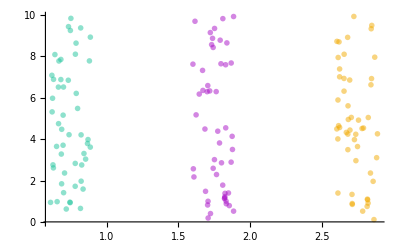

```mathematica
b = ListPlot[Table[ Thread[{Table[RandomReal[ {n-l,n-m} ], Length[a[[n]] ] ], a[[n]] }], {n,1,Length@a}] , PlotMarkers-> {{-Graphics-,mypointsize},{-Graphics-,mypointsize},{-Graphics-,mypointsize}}]
```

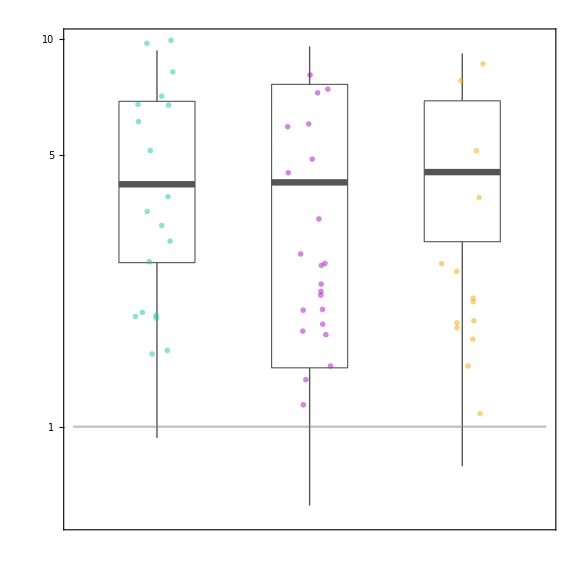

```mathematica
bwchart1 = BoxWhiskerChart[a,{ {"MedianMarker",Directive[Thickness[.008],Darker[Gray]]},{"Whiskers",Directive[Thick,Darker[Gray]]},{"Fences",1,Opacity[0]}} ,ChartStyle->{{EdgeForm[{Darker[Gray], Thickness[Large]}  ]} , {Opacity[0]} } , AspectRatio->1 ,ScalingFunctions->"Log2" ,{Method->{"BoxRange"->(Quantile[#,{.05,.25,.5,.75,.95},{{1,-1},{0,1}}]&)}}];
bwchart2 = BoxWhiskerChart[a,{ {"MedianMarker",Directive[Thickness[.008],Darker[Gray]]},{"Whiskers",Directive[Thick,Darker[Gray]]},{"Fences",1,Opacity[0]}} ,ChartStyle->{{EdgeForm[{Darker[Gray], Thickness[Large]}  ]} , {White} } , AspectRatio->1 ,ScalingFunctions->"Log2" ,{Method->{"BoxRange"->(Quantile[#,{.05,.25,.5,.75,.95},{{1,-1},{0,1}}]&)}}];
myBoxWhiskerPlot1203wctrl =  
Show[   bwchart2,  b,Plot[x=0,{x,0.2,3.3}, PlotStyle->Opacity[0.5,Gray]],bwchart1, AspectRatio -> 1,BaseStyle->{FontFamily->"Arial",FontSize->22},PlotRange-> {-.8,Log2[10]}]
```